```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

```mathematica
<<"./mdat/amps.mdat";
```

## Form Factors

```mathematica
Clear[extractFF];
extractFF::usage="extractFF[json, num]";
extractFF[json_, n_, fact_:1]:=Module[{name, data},
name = json⟦3,2,n,1,2⟧;
data = json⟦3,2,n,5,2,All,3,2⟧;
data⟦All,2⟧=fact*data⟦All,2⟧;
Return[<|"name"->name,"data"->data|>]
]
```

### χ_c(1P)

```mathematica
tab$fPlus = Import["../literatute/Ebert_FFs/chi0_fPlus.csv"];
tab$fMinus = Import["../literatute/Ebert_FFs/chi0_minusFminus.csv"];
tab$fMinus⟦All,2⟧=-tab$fMinus⟦All,2⟧;
```

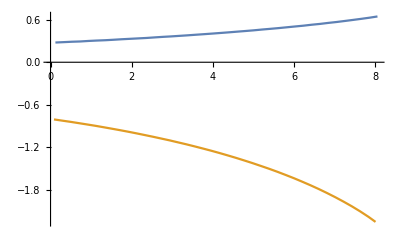

```mathematica
ListPlot[{tab$fPlus, tab$fMinus}, Joined->True]
```

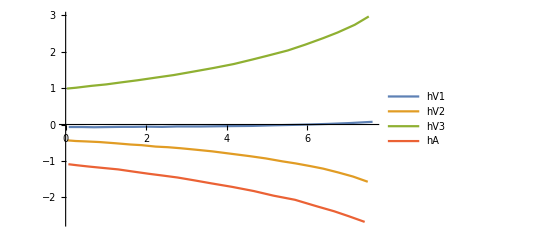

```mathematica
chic1 = Import["../literatute/Ebert_FFs/fig3_chic1_1P.json"];
tab$hV1 = extractFF[chic1,1]["data"];
tab$hV2 = extractFF[chic1,2, -1]["data"];
tab$hV3 = extractFF[chic1,3]["data"];
tab$hA = extractFF[chic1,4,-1]["data"];
ListPlot[{tab$hV1,tab$hV2,tab$hV3, tab$hA}, Joined->True, PlotLegends->{"hV1", "hV2", "hV3", "hA"}]
```

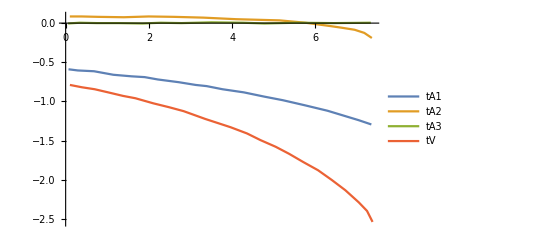

```mathematica
chic2 = Import["../literatute/Ebert_FFs/fig3_chic2_1P.json"];
tab$tA3 = extractFF[chic2, 1]["data"];
tab$tA2 = extractFF[chic2, 2]["data"];
tab$tA1 = extractFF[chic2, 3, -1]["data"];
tab$tV = extractFF[chic2, 4,-1]["data"];
ListPlot[{tab$tA1, tab$tA2, tab$tA3, tab$tV},Joined->True, PlotLegends->{"tA1", "tA2", "tA3", "tV"}, PlotRange->All]
```

### χ_c(2P)

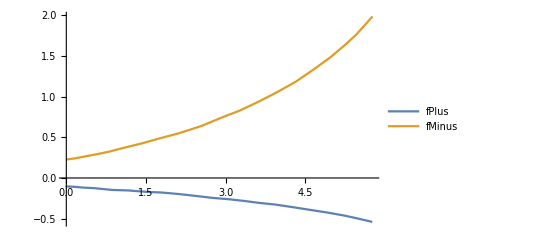

```mathematica
chic0 = Import["../literatute/Ebert_FFs/fig3_chic0_2P.json"];
tab$fPlus$2P = extractFF[chic0,1,-1]["data"];
tab$fMinus$2P = extractFF[chic0,2]["data"];
ListPlot[{tab$fPlus$2P, tab$fMinus$2P}, Joined->True, PlotLegends->{"fPlus", "fMinus"}]
```

{hV1,hV2,hA,-hV3}

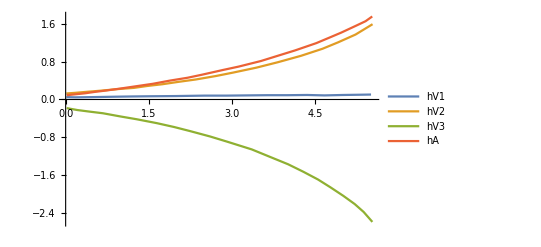

```mathematica
chic1 = Import["../literatute/Ebert_FFs/fig3_chic1_2P.json"];
chic1⟦3,2,All,1,2⟧
tab$hV1$2P = extractFF[chic1,1]["data"];
tab$hV2$2P = extractFF[chic1,2]["data"];
tab$hA$2P = extractFF[chic1,3]["data"];
tab$hV3$2P = extractFF[chic1,4,-1]["data"];
ListPlot[{tab$hV1$2P,tab$hV2$2P,tab$hV3$2P, tab$hA$2P}, Joined->True, PlotLegends->{"hV1", "hV2", "hV3", "hA"}]
```

{tA3,tA2,tA1,tV}

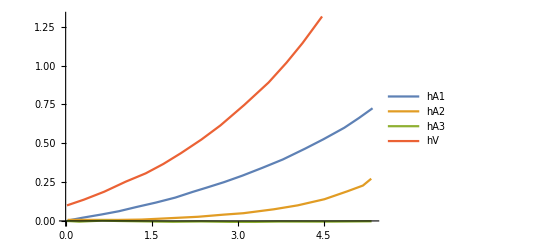

```mathematica
chic2 = Import["../literatute/Ebert_FFs/fig3_chic2_2P.json"];
Print[chic2⟦3,2,All,1,2⟧];
tab$tA3$2P = extractFF[chic2,1]["data"];
tab$tA2$2P = extractFF[chic2,2]["data"];
tab$tA1$2P = extractFF[chic2,3]["data"];
tab$tV$2P = extractFF[chic2,4]["data"];
ListPlot[{tab$tA1$2P,tab$tA2$2P,tab$tA3$2P, tab$tV$2P}, Joined->True, PlotLegends->{"hA1", "hA2", "hA3", "hV"}]
```

```mathematica
fitFunc=a0+a1 q2 + a2 q2^2+a3 q2^3;
fitParams = DeleteCases[Variables[fitFunc] ,q2]
```

{a0,a1,a2,a3}

```mathematica
ffFitRule = Table[
ff[q2_]:>Evaluate[ fitFunc/.FindFit[ToExpression["tab$"<>ToString[ff]], fitFunc,fitParams,q2]]
,{ff, ffList}];
```

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule[[i,2]]/.Power->pow]]<>";\n"
,{i,1,2}];
str
```

*fPlus=0.2735114574549966 + 0.02698177783795792*q2 + 0.0004438591230092838*pow(q2,2) + 0.00023394089715202517*pow(q2,3);
*fMinus=-0.7888608969785541 - 0.10052789894587946*q2 + 0.0028122053015600472*pow(q2,2) - 0.0015941397716725178*pow(q2,3);

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule[[i,2]]/.Power->pow]]<>";\n"
,{i,3,6}];
str
```

*hV1=-0.07249517884406438 + 0.006386114470446252*q2 - 0.0016598461472340164*pow(q2,2) + 0.00043125401922510393*pow(q2,3);
*hV2=-0.42708574288736423 - 0.08150607461417403*q2 + 0.00655250512925111*pow(q2,2) - 0.002089171872485879*pow(q2,3);
*hV3=0.9721190093276546 + 0.14785518940757297*q2 - 0.010128808927653912*pow(q2,2) + 0.0033475878397617523*pow(q2,3);
*hA=-1.0807476041824315 - 0.1250995787006434*q2 + 0.00032468802756664515*pow(q2,2) - 0.0016479191668232192*pow(q2,3);

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule[[i,2]]/.Power->pow]]<>";\n"
,{i,7,10}];
str
```

*tV=-0.7593279619789294 - 0.14373638874539618*q2 + 0.015428531108854306*pow(q2,2) - 0.0037404399820982963*pow(q2,3);
*tA1=-0.5845892322932432 - 0.05829150603138564*q2 + 0.0003828588805250468*pow(q2,2) - 0.0007578111067025861*pow(q2,3);
*tA2=0.0939174867271461 - 0.029819354099933058*q2 + 0.01373975840177015*pow(q2,2) - 0.0019524446633583286*pow(q2,3);
*tA3=-0.0020369655557486233 + 0.0033852618872049524*q2 - 0.0008299552762151167*pow(q2,2) + 0.00006460810519319177*pow(q2,3);

```mathematica
ffFitRule$2P = Table[
ff[q2_]:>Evaluate[ fitFunc/.FindFit[ToExpression["tab$"<>ToString[ff]<>"$2P"], fitFunc,fitParams,q2]]
,{ff, ffList}];
```

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule$2P⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule$2P[[i,2]]/.Power->pow]]<>";\n"
,{i,1,2}];
str
```

*fPlus=-0.1036523606752476 - 0.04296031595098163*q2 + 0.0006186521497841605*pow(q2,2) - 0.0010752967931538292*pow(q2,3);
*fMinus=0.2146487305494538 + 0.15242330361247391*q2 - 0.010551275203077543*pow(q2,2) + 0.006370594008633078*pow(q2,3);

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule$2P⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule$2P[[i,2]]/.Power->pow]]<>";\n"
,{i,3,6}];
str
```

*hV1=0.04439115389660447 + 0.019084131704071243*q2 - 0.002604726424031802*pow(q2,2) + 0.00018149830649920272*pow(q2,3);
*hV2=0.1172598023033568 + 0.12069109270869871*q2 - 0.012606920768015749*pow(q2,2) + 0.006864162691296876*pow(q2,3);
*hV3=-0.16364417143981633 - 0.22885046487359123*q2 + 0.030520612375782352*pow(q2,2) - 0.012027948054465212*pow(q2,3);
*hA=0.07973359107787653 + 0.15842249566142913*q2 - 0.005579327065777525*pow(q2,2) + 0.00560617437583373*pow(q2,3);

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule$2P⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule$2P[[i,2]]/.Power->pow]]<>";\n"
,{i,7,10}];
str
```

*tV=0.09539971009568 + 0.1323082354062854*q2 + 0.007744430814653726*pow(q2,2) + 0.0052822727875911765*pow(q2,3);
*tA1=-0.0014086383044029733 + 0.06739181582166379*q2 + 0.0036492170862357574*pow(q2,2) + 0.0016746836655900166*pow(q2,3);
*tA2=0.0017971881442419284 + 0.01760619468206874*q2 - 0.010590128853260362*pow(q2,2) + 0.0030609488394743095*pow(q2,3);
*tA3=-0.0008750946774129126 - 0.0005646397692624229*q2 - 0.0007184243134305922*pow(q2,2) + 0.0001459108759474624*pow(q2,3);

## Save

```mathematica
DeleteFile["./mdat/ebert_ff.mdat"];
file = OpenWrite["./mdat/ebert_ff.mdat"];
WriteString[file, ToString[Definition[ffFitRule], InputForm]<>"\n"];
WriteString[file, ToString[Definition[ffFitRule$2P], InputForm]<>"\n"];
Close[file];
```